# Mathematica Notebook for Reproducing the Results for the Paper “Too little, too late -- a dynamical systems model for gun-related violence and intervention” by Feng Fu and Dan Rockmore

```mathematica
Clear["`*"]
```

```mathematica
(*growth rate of gun prevalence*)
a=0.2;
(*ceiling rate of gun prevalence*)
k=1;
(*gun violence rate curvature parameter*)
θ=1;
(*ceiling of gun violence rate and scaling factor*)
c=5000/100000;
(*interventiondecision threshold*)
τ=1000/100000;
(*intervention intensity*)
b=0.2;
b0=0;
```

```mathematica
(*free gun diffusion equation*)
f[x_]:=a x (k-x);
```

```mathematica
(*interventions curbing guns as function of gun prevalence x, gun violence Ig = cx^theta*)
```

```mathematica
Stoppoly[x_,b_,n_,τ_]:=b0+(b-b0) ((c x^θ)^n/(τ^n + (c x^θ)^n));
```

## Bifurcation diagrams regarding impacts of the critical threshold τ and intervention response parameter n

```mathematica
(*response is steady and increasing with gun violence, n = 1*)
```

```mathematica
Manipulate[ContourPlot[f[x]==Stoppoly[x,b,1,τ],{b,0,0.2},{x,0,1},Frame->True,FrameLabel->{"Intervention strength","Gun prevalence"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1/2,FrameStyle->Directive[Black,Thickness[0.002]],MaxRecursion->5],{τ,0,1000/100000}]
```

```mathematica
(*response is step function like, n = 49*)
```

```mathematica
Manipulate[ContourPlot[f[x]==Stoppoly[x,b,49,τ],{b,0,0.2},{x,0,1},Frame->True,FrameLabel->{"Intervention strength","Gun prevalence"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1/2,FrameStyle->Directive[Black,Thickness[0.002]],MaxRecursion->5],{τ,0,1000/100000}]
```

# Figure 1

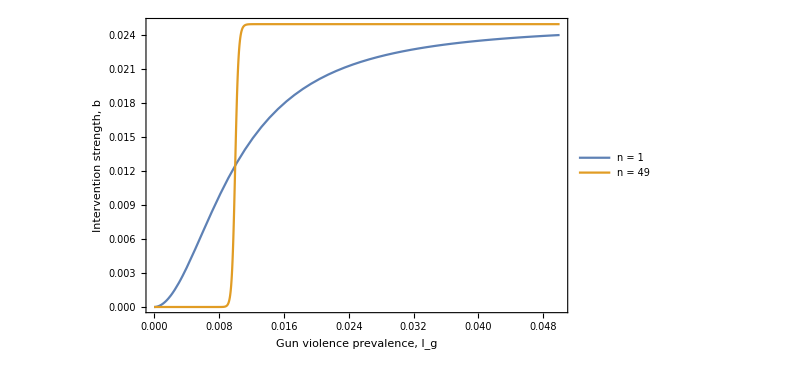

```mathematica
(*intervention response as function of gun violence rate Ig*)
Stoppoly2[x_,b_,n_]:=b (1/((τ/x)^n +1));
Figsig=Plot[{Stoppoly2[x,25/1000,2],Stoppoly2[x,25/1000,49]},{x,0,5000/100000},PlotRange->All,Frame->True,FrameLabel->{"Gun violence prevalence, I_g","Intervention strength, b"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1/GoldenRatio,FrameStyle->Directive[Black,Thickness[0.002]],PlotLegends->Placed[{"n = 1","n = 49"},{Right,Bottom}]]
```

# Figure 2

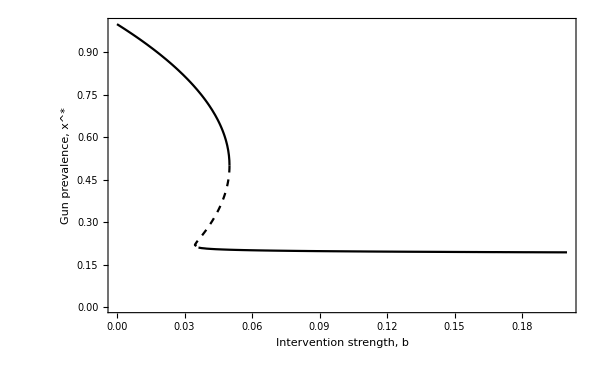

```mathematica
fig2a=ContourPlot[f[x]==Stoppoly[x,b,49,τ],{b,0,0.2},{x,0.5,1},ContourStyle->{Black}];
fig2b=ContourPlot[f[x]==Stoppoly[x,b,49,τ],{b,0,0.2},{x,0.21,0.5},ContourStyle->{Dashed,Black}];
fig2c=ContourPlot[f[x]==Stoppoly[x,b,49,τ],{b,0,0.2},{x,0,0.21},ContourStyle->{Black}];
Fig2=Show[fig2a,fig2b,fig2c,PlotRange->{{0,0.2},{0,1}},Frame->True,FrameLabel->{"Intervention strength, b","Gun prevalence, x^*"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1/GoldenRatio,FrameStyle->Directive[Black,Thickness[0.002]]]
```

# Figure 3

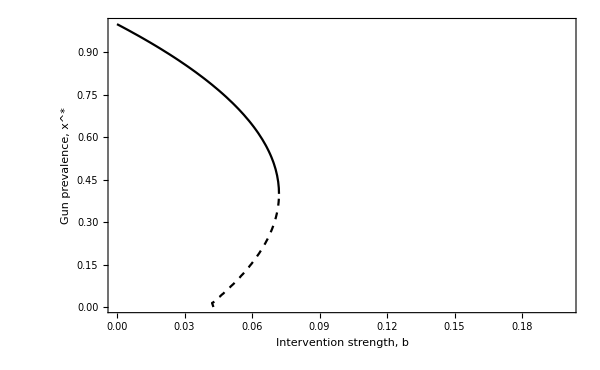

```mathematica
fig1a=ContourPlot[f[x]==Stoppoly[x,b,1,τ],{b,0,0.2},{x,0.4,1},ContourStyle->{Black}];
fig1b=ContourPlot[f[x]==Stoppoly[x,b,1,τ],{b,0,0.2},{x,0,0.4},ContourStyle->{Dashed,Black}];
Fig1=Show[fig1a,fig1b,PlotRange->{{0,0.2},{0,1}},Frame->True,FrameLabel->{"Intervention strength, b","Gun prevalence, x^*"},FrameTicksStyle->Directive[FontSize->20,Black],LabelStyle->Directive[FontSize->20,Black],ImageSize->600,AspectRatio->1/GoldenRatio,FrameStyle->Directive[Black,Thickness[0.002]]]
```